# Lab 4: Competition

## Lotka-Volterra Competition

Consider two competing populations that follow the Lotka-Volterra competition equations

dn_1/dt=r_1 n_1(1-n_1/k_1-α_12 n_2/k_1)
dn_2/dt=r_2 n_2(1-n_2/k_2-α_21 n_1/k_2)

### Solve for equilibria analytically. How many are they and what do they represent?

There are four equilibria.  The first one is where species 1 is nonexistant and species 2 goes to carrying capacity.  The second is the coexistence point. The third one is where both species don’t exist.  The fourth one is where species 1 goes to carrying capacity and species 2 is nonexistant.

```mathematica
(* set up right hand sides *)


f1:=r1*n1*(1-n1/k1-α12*n2/k1);
f2:=r2*n2*(1-n2/k2-α21*n1/k2);
```

```mathematica
(* solve for equilibria *)

eq=Solve[{f1==0,f2==0},{n1,n2}]
```

{{n1→0,n2→k2},{n1→-(k1-k2 α12)/(-1+α12 α21),n2→-(k2-k1 α21)/(-1+α12 α21)},{n1→0,n2→0},{n1→k1,n2→0}}

### Find the Jacobian matrix

```mathematica
j:=D[{f1,f2},{{n1,n2}}];
j//MatrixForm
```

(-(n1 r1)/k1+r1 (1-n1/k1-(n2 α12)/k1) | -(n1 r1 α12)/k1
-(n2 r2 α21)/k2 | -(n2 r2)/k2+r2 (1-n2/k2-(n1 α21)/k2))

### Evaluate the Jacobian at all of the different equilibria. Derive analytical conditions for the stability of the boundary equilibria and interpret them biologically.

```mathematica
j/.eq[[1]]//MatrixForm
```

(r1 (1-(k2 α12)/k1) | 0
-r2 α21 | -r2)

```mathematica
({{1-(k2 α12)/k1, 0}, {-α21, -1}})
```

{{1-(k2 α12)/k1,0},{-α21,-1}}

```mathematica
Eigenvalues[j/.eq[[1]]]
```

{-r2,r1 (1-(k2 α12)/k1)}

```mathematica
{-1,1-(k2 α12)/k1}
```

{-1,1-(k2 α12)/k1}

If (k2 α12)/k1is greater than one, then this point will be stable, otherwise it would be unstable.  Biologically, if the growth rate of species 1 when it’s rare is enough to invade species 2 when it’s at its carrying capacity, then this point would not be stable.

```mathematica
j/.eq[[3]]//MatrixForm
```

(r1 | 0
0 | r2)

```mathematica
Eigenvalues[j/.eq[[3]]]
```

{r1,r2}

This equilibrium point is unstable because both values are above 1.  Biologically, any perturbation would move the trajectories away from this equilibrium point.  This equil

```mathematica
j/.eq[[4]]//MatrixForm
```

(-r1 | -r1 α12
0 | r2 (1-(k1 α21)/k2))

```mathematica
Eigenvalues[j/.eq[[4]]]
```

{-r1,r2 (1-(k1 α21)/k2)}

If (k1 α21)/k2is greater than one, then this point will be stable, otherwise it would be unstable.  Biologically, if the growth rate of species 2 when it’s rare is enough to invade species 1 when it’s at its carrying capacity, then this point would not be stable.

### Numerically solve the model for five different sets of parameters to illustrate the five possible outcomes (1 beats 2, 2 beats 1, 1 and 2 coexist, founder control, equivalent species). Code is provided, just add parameters. Use multiple different initial conditions to show different outcomes if they exist (founder control, equivalent species). Then verify equilibrium densities and eigenvalues numerically.

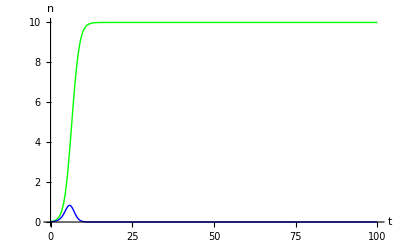

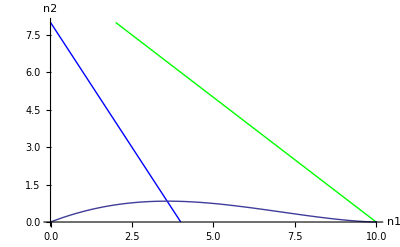

```mathematica
tmax=100; (* how long to run *)

(* parameters *)

r1=1;
r2=1;
k1=10;
k2=8;
α12=1;
α21=2;

(* initial population sizes *)

n10=0.02;
n20=0.01;

(* numerically solve model *)

sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1-α12*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2-α21*n1[t]/k2),
n1[0]==n10,
n2[0]==n20},{n1,n2},{t,0,tmax}];

(* plot n1 (green) and n2 (blue) vs t *)

Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax},PlotStyle->{Green,Blue},PlotRange->All,AxesLabel->{"t","n"}]

(* plot isoclines and n2 vs n1 *)

isoplot=Plot[{k1/α12-n1/α12,k2-α21*n1},{n1,0,k1},PlotStyle->{Green,Blue},PlotRange->{0,k2}];
dynplot=ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax}];
Show[isoplot,dynplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,k1},{0,k2}},AxesLabel->{"n1","n2"}]
```

This means that species 1 wins.  This is case 1.

```mathematica
(* evaluate equilibria numerically *)

eq
```

{{n1→0,n2→8},{n1→-2,n2→12},{n1→0,n2→0},{n1→10,n2→0}}

```mathematica
(* eigenvalues for eq #1 *)

Eigenvalues[j/.eq[[1]]]
```

{-1,1/5}

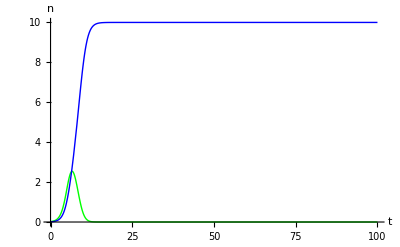

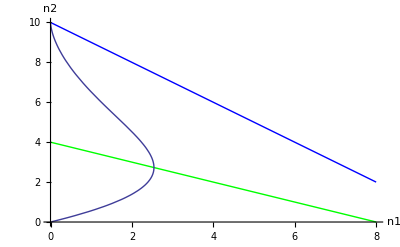

```mathematica
Clear[r1, r2, k1, k2, α12, α21]
tmax=100; (* how long to run *)

(* parameters *)

r1=1;
r2=1;
k1=8;
k2=10;
α12=2;
α21=1;

(* initial population sizes *)

n10=0.02;
n20=0.01;

(* numerically solve model *)

sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1-α12*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2-α21*n1[t]/k2),
n1[0]==n10,
n2[0]==n20},{n1,n2},{t,0,tmax}];

(* plot n1 (green) and n2 (blue) vs t *)

Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax},PlotStyle->{Green,Blue},PlotRange->All,AxesLabel->{"t","n"}]

(* plot isoclines and n2 vs n1 *)

isoplot=Plot[{k1/α12-n1/α12,k2-α21*n1},{n1,0,k1},PlotStyle->{Green,Blue},PlotRange->{0,k2}];
dynplot=ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax}];
Show[isoplot,dynplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,k1},{0,k2}},AxesLabel->{"n1","n2"}]

eq

(* eigenvalues for eq #1 *)

Eigenvalues[j/.eq[[1]]]
```

This is case 2.  Species 2 wins.

{{n1→0,n2→10},{n1→12,n2→-2},{n1→0,n2→0},{n1→8,n2→0}}

These are the equilibrium points and below Eigen values

{-3/2,-1}

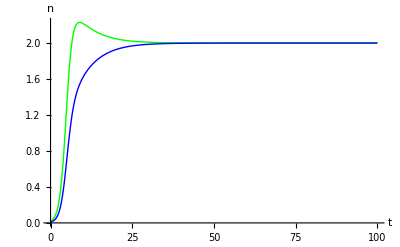

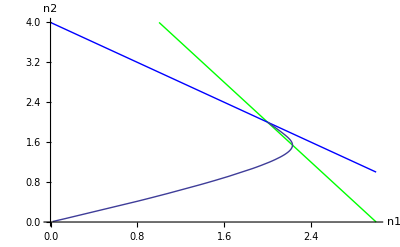

```mathematica
Clear[r1, r2, k1, k2, α12, α21]
tmax=100; (* how long to run *)

(* parameters *)

r1=1;
r2=1;
k1=3;
k2=4;
α12=0.5;
α21=1;

(* initial population sizes *)

n10=0.02;
n20=0.01;

(* numerically solve model *)

sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1-α12*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2-α21*n1[t]/k2),
n1[0]==n10,
n2[0]==n20},{n1,n2},{t,0,tmax}];

(* plot n1 (green) and n2 (blue) vs t *)

Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax},PlotStyle->{Green,Blue},PlotRange->All,AxesLabel->{"t","n"}]

(* plot isoclines and n2 vs n1 *)

isoplot=Plot[{k1/α12-n1/α12,k2-α21*n1},{n1,0,k1},PlotStyle->{Green,Blue},PlotRange->{0,k2}];
dynplot=ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax}];
Show[isoplot,dynplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,k1},{0,k2}},AxesLabel->{"n1","n2"}]

eq

(* eigenvalues for eq #1 *)

Eigenvalues[j/.eq[[1]]]
```

They coexist.  Awesome.  This is case 3.

{{n1→0,n2→4},{n1→2.,n2→2.},{n1→0,n2→0},{n1→3,n2→0}}

These are the equilibrium points and below Eigen values

{-1.,0.333333}

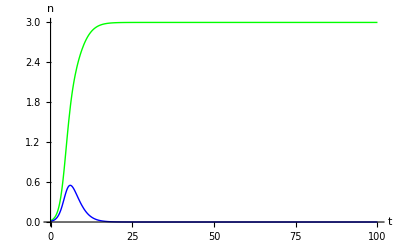

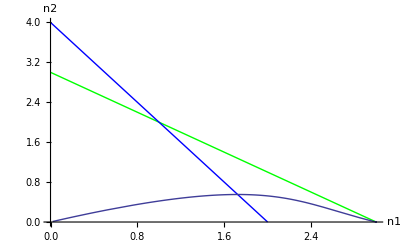

```mathematica
tmax=100; (* how long to run *)

(* parameters *)

r1=1;
r2=1;
k1=3;
k2=4;
α12=1;
α21=2;

(* initial population sizes *)

n10=0.02;
n20=0.01;

(* numerically solve model *)

sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1-α12*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2-α21*n1[t]/k2),
n1[0]==n10,
n2[0]==n20},{n1,n2},{t,0,tmax}];

(* plot n1 (green) and n2 (blue) vs t *)

Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax},PlotStyle->{Green,Blue},PlotRange->All,AxesLabel->{"t","n"}]

(* plot isoclines and n2 vs n1 *)

isoplot=Plot[{k1/α12-n1/α12,k2-α21*n1},{n1,0,k1},PlotStyle->{Green,Blue},PlotRange->{0,k2}];
dynplot=ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax}];
Show[isoplot,dynplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,k1},{0,k2}},AxesLabel->{"n1","n2"}]

eq

(* eigenvalues for eq #1 *)

Eigenvalues[j/.eq[[1]]]
```

This is case four, founder control.  In the plot being shown, species 1 starts at the higher amount so it wins because started off at higher densities.

{{n1→0,n2→4},{n1→1,n2→2},{n1→0,n2→0},{n1→3,n2→0}}

These are the equilibrium points and below Eigen values

{-1,-1/3}

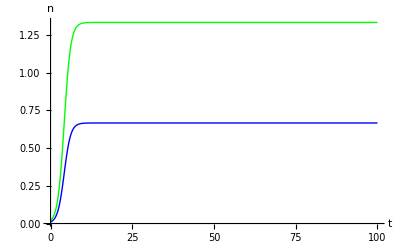

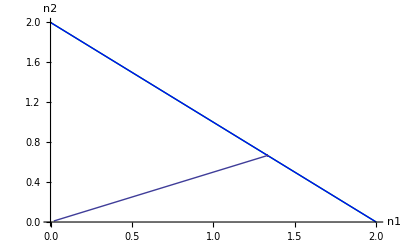

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

```mathematica
tmax=100; (* how long to run *)

(* parameters *)

r1=1;
r2=1;
k1=2;
k2=2;
α12=1;
α21=1;

(* initial population sizes *)

n10=0.02;
n20=0.01;

(* numerically solve model *)

sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1-α12*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2-α21*n1[t]/k2),
n1[0]==n10,
n2[0]==n20},{n1,n2},{t,0,tmax}];

(* plot n1 (green) and n2 (blue) vs t *)

Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax},PlotStyle->{Green,Blue},PlotRange->All,AxesLabel->{"t","n"}]

(* plot isoclines and n2 vs n1 *)

isoplot=Plot[{k1/α12-n1/α12,k2-α21*n1},{n1,0,k1},PlotStyle->{Green,Blue},PlotRange->{0,k2}];
dynplot=ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,tmax}];
Show[isoplot,dynplot,DisplayFunction->$DisplayFunction,PlotRange->{{0,k1},{0,k2}},AxesLabel->{"n1","n2"}]

eq

(* eigenvalues for eq #1 *)

Eigenvalues[j/.eq[[1]]]
```

This is case 5, there are an infinite number of equilibria (as seen below with the “indeterminates”).  This is called neutrally stable/equivalent species.

{{n1→0,n2→2},{n1→Indeterminate,n2→Indeterminate},{n1→0,n2→0},{n1→2,n2→0}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{-1,0}

## Bonus: Three species intransitive Lotka-Volterra competition

### Use Mathematica to replicate the numerical results from following paper (on web) : May and Leonard 1975. Nonlinear aspects of comptition between three species. SIAM Journal on Applied Mathemetics 29: 243-253.